```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"tooth_naive.xml"];*)
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
epsilon=0.01;
stepsize=0.05;
```

{0.1,0.3,0.6}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*(* prototype first-order and second-order methods *)
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];(*should be second-order but look like first-order*)
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient,square,direction},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
square=(mean-target)^2;
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,g0,s0,dy,dx},
{rms0,mean0,p0,g0,s0}=previous;
dy=square-s0;
dx=gradient-g0;
If[Product[i,{i,dx}]≠0,direction=dy/dx;-dy/dx*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks,gradient,square};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,direction}
],{iterator,73}];
```

5.7333916

72

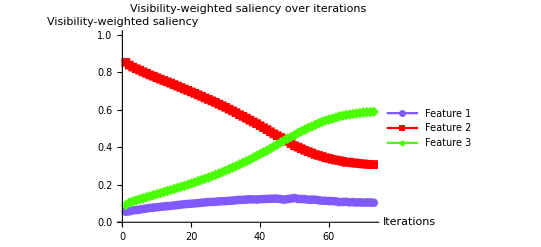

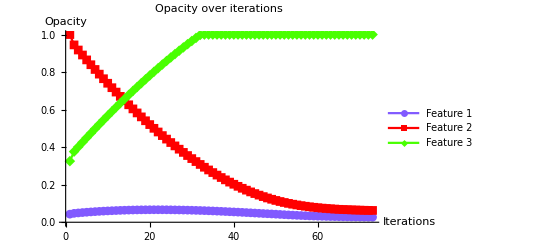

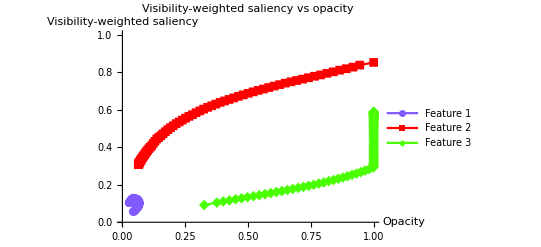

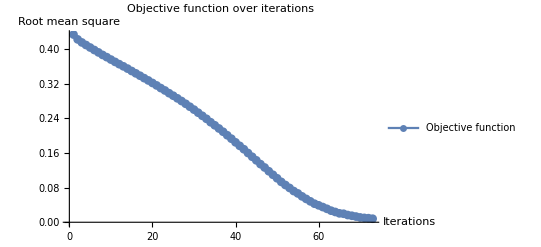

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | direction$480432
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00212956
-0.0272172
0.0250876 | -0.0425912
0.544343
-0.501752
3 | 0.0626292
0.826528
0.110843 | 0.0496014
0.917629
0.401397 | 0.415493 | 0.00198017
-0.0265918
0.0246116 | -0.0396035
0.531836
-0.492232
4 | 0.0654647
0.817971
0.116565 | 0.0515816
0.891037
0.426009 | 0.409551 | 0.00179765
-0.0261125
0.0243148 | -0.035953
0.522249
-0.486296
5 | 0.0673297
0.810056
0.122614 | 0.0533793
0.864924
0.450324 | 0.403783 | 0.00168014
-0.0257007
0.0240205 | -0.0336028
0.514013
-0.48041
6 | 0.0708165
0.801423
0.127761 | 0.0550594
0.839224
0.474344 | 0.398031 | 0.00154635
-0.025287
0.0237406 | -0.0309269
0.505739
-0.474813
7 | 0.0731675
0.79352
0.133313 | 0.0566057
0.813937
0.498085 | 0.392462 | 0.0014004
-0.0248736
0.0234732 | -0.028008
0.497471
-0.469463
8 | 0.0762825
0.784888
0.138829 | 0.0580061
0.789063
0.521558 | 0.386591 | 0.00126375
-0.0244602
0.0231965 | -0.025275
0.489204
-0.463929
9 | 0.0778096
0.777894
0.144297 | 0.0592699
0.764603
0.544755 | 0.381462 | 0.0011477
-0.0240696
0.0229219 | -0.022954
0.481391
-0.458437
10 | 0.0799996
0.77006
0.14994 | 0.0604176
0.740533
0.567677 | 0.375903 | 0.00105477
-0.0236988
0.0226441 | -0.0210954
0.473977
-0.452881
11 | 0.0823675
0.762394
0.155238 | 0.0614724
0.716834
0.590321 | 0.370555 | 0.000940823
-0.0233114
0.0223705 | -0.0188165
0.466227
-0.447411
12 | 0.0837819
0.755289
0.16093 | 0.0624132
0.693523
0.612691 | 0.365301 | 0.000846266
-0.0229421
0.0220958 | -0.0169253
0.458841
-0.441916
13 | 0.0854584
0.748369
0.166173 | 0.0632594
0.670581
0.634787 | 0.360302 | 0.000768993
-0.0225914
0.0218224 | -0.0153799
0.451829
-0.436449
14 | 0.0871895
0.741114
0.171697 | 0.0640284
0.64799
0.656609 | 0.355053 | 0.000683803
-0.0222371
0.0215533 | -0.0136761
0.444741
-0.431065
15 | 0.0894998
0.73311
0.17739 | 0.0647122
0.625753
0.678163 | 0.349425 | 0.000582768
-0.0218556
0.0212728 | -0.0116554
0.437112
-0.425457
16 | 0.0916254
0.725496
0.182878 | 0.065295
0.603897
0.699435 | 0.344048 | 0.000471869
-0.0214652
0.0209933 | -0.00943738
0.429303
-0.419866
17 | 0.0939055
0.717715
0.18838 | 0.0657669
0.582432
0.720429 | 0.338602 | 0.000361725
-0.0210803
0.0207186 | -0.0072345
0.421606
-0.414371
18 | 0.0961694
0.709772
0.194059 | 0.0661286
0.561352
0.741147 | 0.333025 | 0.000248127
-0.0206872
0.020439 | -0.00496253
0.413743
-0.408781
19 | 0.0975699
0.702529
0.199902 | 0.0663767
0.540664
0.761586 | 0.327676 | 0.000156518
-0.0203075
0.020151 | -0.00313036
0.40615
-0.40302
20 | 0.0989591
0.694723
0.206318 | 0.0665333
0.520357
0.781737 | 0.321866 | 0.000086776
-0.0199313
0.0198445 | -0.00173552
0.398626
-0.39689
21 | 0.100464
0.686995
0.21254 | 0.06662
0.500426
0.801582 | 0.31617 | 0.0000144169
-0.019543
0.0195285 | -0.000288338
0.390859
-0.390571
22 | 0.102156
0.678634
0.219211 | 0.0666344
0.480883
0.82111 | 0.310037 | -0.0000654991
-0.0191407
0.0192062 | 0.00130998
0.382815
-0.384125
23 | 0.103838
0.671023
0.225139 | 0.0665689
0.461742
0.840317 | 0.304518 | -0.000149837
-0.0187414
0.0188913 | 0.00299673
0.374829
-0.377825
24 | 0.105721
0.662348
0.231932 | 0.0664191
0.443
0.859208 | 0.298218 | -0.00023896
-0.0183343
0.0185732 | 0.0047792
0.366685
-0.371465
25 | 0.107525
0.654292
0.238183 | 0.0661801
0.424666
0.877781 | 0.292399 | -0.000331129
-0.017916
0.0182471 | 0.00662259
0.35832
-0.364942
26 | 0.108296
0.646451
0.245252 | 0.065849
0.40675
0.896028 | 0.286323 | -0.000395524
-0.0175186
0.0179141 | 0.00791048
0.350372
-0.358282
27 | 0.109008
0.638479
0.252513 | 0.0654535
0.389232
0.913942 | 0.280117 | -0.000432621
-0.0171233
0.0175559 | 0.00865243
0.342465
-0.351117
28 | 0.111031
0.629584
0.259385 | 0.0650209
0.372108
0.931498 | 0.273719 | -0.000500979
-0.0167016
0.0172026 | 0.0100196
0.334032
-0.344051
29 | 0.112181
0.620669
0.26715 | 0.0645199
0.355407
0.948701 | 0.266937 | -0.000580282
-0.0162563
0.0168366 | 0.0116056
0.325127
-0.336732
30 | 0.11259
0.612248
0.275162 | 0.0639396
0.33915
0.965537 | 0.260241 | -0.000619275
-0.0158229
0.0164422 | 0.0123855
0.316458
-0.328844
31 | 0.114113
0.602761
0.283125 | 0.0633203
0.323328
0.98198 | 0.253162 | -0.000667595
-0.0153752
0.0160428 | 0.0133519
0.307504
-0.320856
32 | 0.115404
0.593265
0.291332 | 0.0626527
0.307952
0.998022 | 0.245979 | -0.000737921
-0.0149007
0.0156386 | 0.0147584
0.298013
-0.312772
33 | 0.117285
0.583717
0.298998 | 0.0619148
0.293052
1. | 0.239023 | -0.000817212
-0.0144245
0.0152418 | 0.0163442
0.288491
-0.304835
34 | 0.119244
0.57298
0.307776 | 0.0610976
0.278627
1. | 0.231144 | -0.000913213
-0.0139174
0.0148306 | 0.0182643
0.278348
-0.296613
35 | 0.119576
0.564125
0.316299 | 0.0601844
0.26471
1. | 0.224077 | -0.000970498
-0.0134276
0.0143981 | 0.01941
0.268553
-0.287962
36 | 0.120763
0.554392
0.324845 | 0.0592139
0.251282
1. | 0.216685 | -0.00100849
-0.0129629
0.0139714 | 0.0201697
0.259258
-0.279428
37 | 0.12229
0.544267
0.333443 | 0.0582054
0.238319
1. | 0.209137 | -0.00107633
-0.0124665
0.0135428 | 0.0215266
0.249329
-0.270856
38 | 0.121767
0.534586
0.343647 | 0.0571291
0.225853
1. | 0.201015 | -0.00110143
-0.0119713
0.0130727 | 0.0220285
0.239426
-0.261455
39 | 0.121069
0.525228
0.353703 | 0.0560277
0.213881
1. | 0.193075 | -0.00107089
-0.0114953
0.0125662 | 0.0214177
0.229907
-0.251325
40 | 0.122797
0.513904
0.363299 | 0.0549568
0.202386
1. | 0.184664 | -0.00109664
-0.0109783
0.012075 | 0.0219329
0.219566
-0.241499
41 | 0.123269
0.503693
0.373037 | 0.0538601
0.191408
1. | 0.176583 | -0.00115167
-0.0104399
0.0115916 | 0.0230333
0.208799
-0.231832
42 | 0.124558
0.49332
0.382123 | 0.0527085
0.180968
1. | 0.168766 | -0.00119568
-0.00992532
0.011121 | 0.0239135
0.198506
-0.22242
43 | 0.125055
0.482198
0.392747 | 0.0515128
0.171042
1. | 0.159977 | -0.00124032
-0.00938794
0.0106283 | 0.0248064
0.187759
-0.212565
44 | 0.125758
0.471094
0.403149 | 0.0502725
0.161655
1. | 0.151313 | -0.00127032
-0.0088323
0.0101026 | 0.0254064
0.176646
-0.202052
45 | 0.125897
0.460817
0.413285 | 0.0490021
0.152822
1. | 0.143056 | -0.00129137
-0.00829778
0.00958915 | 0.0258274
0.165956
-0.191783
46 | 0.123386
0.451527
0.425087 | 0.0477108
0.144524
1. | 0.134291 | -0.00123207
-0.00780861
0.00904069 | 0.0246415
0.156172
-0.180814
47 | 0.120621
0.443654
0.435726 | 0.0464787
0.136716
1. | 0.126554 | -0.00110016
-0.00737952
0.00847968 | 0.0220033
0.14759
-0.169594
48 | 0.123347
0.431359
0.445295 | 0.0453785
0.129336
1. | 0.117946 | -0.00109918
-0.00687531
0.00797449 | 0.0219836
0.137506
-0.15949
49 | 0.126012
0.419441
0.454546 | 0.0442794
0.122461
1. | 0.109696 | -0.00123398
-0.00627
0.00750398 | 0.0246795
0.1254
-0.15008
50 | 0.128704
0.407606
0.46369 | 0.0430454
0.116191
1. | 0.101626 | -0.00136792
-0.00567617
0.00704409 | 0.0273584
0.113523
-0.140882
51 | 0.124496
0.399996
0.475508 | 0.0416775
0.110515
1. | 0.0932696 | -0.00133002
-0.00519004
0.00652006 | 0.0266003
0.103801
-0.130401
52 | 0.123628
0.391589
0.484783 | 0.0403474
0.105325
1. | 0.0860656 | -0.0012031
-0.00478964
0.00599274 | 0.024062
0.0957928
-0.119855
53 | 0.123376
0.383241
0.493383 | 0.0391443
0.100535
1. | 0.0792521 | -0.0011751
-0.00437075
0.00554586 | 0.023502
0.0874151
-0.110917
54 | 0.120228
0.376422
0.503349 | 0.0379692
0.0961644
1. | 0.07209 | -0.00109012
-0.00399157
0.00508169 | 0.0218024
0.0798315
-0.101634
55 | 0.12078
0.36919
0.510029 | 0.0368791
0.0921728
1. | 0.0666181 | -0.00102522
-0.00364032
0.00466554 | 0.0205044
0.0728063
-0.0933108
56 | 0.120385
0.360899
0.518716 | 0.0358539
0.0885325
1. | 0.0598087 | -0.00102912
-0.00325224
0.00428136 | 0.0205825
0.0650448
-0.0856272
57 | 0.117238
0.35578
0.526983 | 0.0348248
0.0852802
1. | 0.0539754 | -0.000940553
-0.00291697
0.00385752 | 0.0188111
0.0583394
-0.0771505
58 | 0.114544
0.350542
0.534913 | 0.0338842
0.0823633
1. | 0.0483128 | -0.000794551
-0.00265806
0.00345261 | 0.015891
0.0531611
-0.0690521
59 | 0.114217
0.34392
0.541863 | 0.0330897
0.0797052
1. | 0.0428604 | -0.000719029
-0.00236157
0.0030806 | 0.0143806
0.0472314
-0.061612
60 | 0.112952
0.340083
0.546965 | 0.0323707
0.0773436
1. | 0.0391028 | -0.000679222
-0.00210008
0.0027793 | 0.0135844
0.0420016
-0.055586
61 | 0.112748
0.335186
0.552066 | 0.0316914
0.0752436
1. | 0.0351103 | -0.000642504
-0.00188172
0.00252422 | 0.0128501
0.0376343
-0.0504844
62 | 0.111314
0.331122
0.557565 | 0.0310489
0.0733619
1. | 0.0310769 | -0.000601548
-0.00165769
0.00225923 | 0.012031
0.0331537
-0.0451847
63 | 0.107522
0.328337
0.564141 | 0.0304474
0.0717042
1. | 0.026742 | -0.000470902
-0.00148645
0.00195736 | 0.00941804
0.0297291
-0.0391471
64 | 0.108238
0.324102
0.56766 | 0.0299765
0.0702177
1. | 0.0237674 | -0.000393996
-0.00131097
0.00170497 | 0.00787992
0.0262195
-0.0340994
65 | 0.109041
0.319461
0.571497 | 0.0295825
0.0689067
1. | 0.0205984 | -0.000431978
-0.00108909
0.00152107 | 0.00863956
0.0217818
-0.0304213
66 | 0.10629
0.3203
0.57341 | 0.0291505
0.0678176
1. | 0.0196529 | -0.000383293
-0.000994032
0.00137732 | 0.00766586
0.0198806
-0.0275465
67 | 0.107013
0.315992
0.576995 | 0.0287672
0.0668236
1. | 0.0166747 | -0.000332585
-0.000907294
0.00123988 | 0.0066517
0.0181459
-0.0247976
68 | 0.105409
0.315047
0.579544 | 0.0284346
0.0659163
1. | 0.0149903 | -0.000310543
-0.000775977
0.00108652 | 0.00621087
0.0155195
-0.0217304
69 | 0.105868
0.312349
0.581784 | 0.0281241
0.0651403
1. | 0.0131497 | -0.000281905
-0.000684899
0.000966804 | 0.00563809
0.013698
-0.0193361
70 | 0.104814
0.310572
0.584614 | 0.0278422
0.0644554
1. | 0.0111303 | -0.000267044
-0.000573002
0.000840046 | 0.00534088
0.01146
-0.0168009
71 | 0.105091
0.308928
0.585982 | 0.0275751
0.0638824
1. | 0.0100356 | -0.000247619
-0.000487486
0.000735105 | 0.00495237
0.00974973
-0.0147021
72 | 0.105271
0.307924
0.586805 | 0.0273275
0.063395
1. | 0.00939319 | -0.000259037
-0.000421309
0.000680346 | 0.00518073
0.00842618
-0.0136069
73 | 0.104098
0.307306
0.588595 | 0.0270685
0.0629737
1. | 0.00817012 | -0.000234235
-0.00038077
0.000615006 | 0.0046847
0.00761541
-0.0123001

```mathematica
t2-t1
iteration
saliency5=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_newton.png",saliency5];
opacity5=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_newton.png",opacity5];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity5=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_newton.png",saliencyopacity5];
rms5=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_newton.png",rms5];
table5=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_newton.png",table5];
path5=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path5]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
previous={0,{0,0,0},{0,0,0}};
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,gradient},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
gradient:=2*(mean-target);
(*steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=rms-Table[RootMeanSquare[Table[If[i==n,mean0[[i]],mean[[i]]],{i,Length[mean]}]-target],{n,Length[mean]}];
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*stepsize,-gradient*stepsize]
]];*)
steps=If[First@previous==0,-gradient*stepsize,Module[{rms0,mean0,p0,dy,dx},
{rms0,mean0,p0}=previous;
dy=mean-mean0;
dx=peaks-p0;
If[Product[i,{i,dx}]≠0,-dy/dx*gradient*stepsize,-gradient*stepsize]
]];
previous={rms,mean,peaks};
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,52}];
```

4.0059134

51

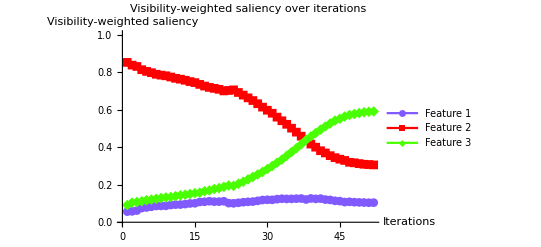

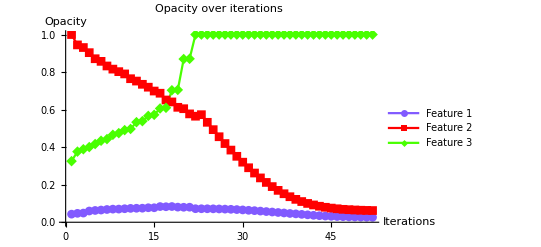

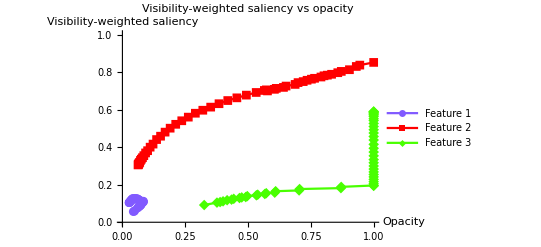

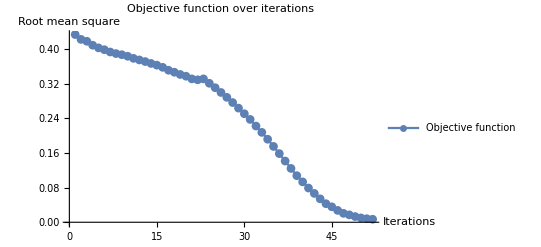

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00145742
-0.014024
0.0125629
3 | 0.0624131
0.829913
0.107674 | 0.0489293
0.930822
0.388873 | 0.418173 | 0.0109589
-0.0273216
0.0116832
4 | 0.0757834
0.812669
0.111548 | 0.0598882
0.9035
0.400556 | 0.409064 | 0.00295453
-0.0323571
0.0161953
5 | 0.0788751
0.803702
0.117423 | 0.0628427
0.871143
0.416751 | 0.402924 | 0.00221055
-0.0139583
0.0175057
6 | 0.0825861
0.796776
0.120638 | 0.0650532
0.857185
0.434257 | 0.398697 | 0.00292344
-0.0246491
0.00880304
7 | 0.0867927
0.788334
0.124873 | 0.0679767
0.832536
0.44306 | 0.393442 | 0.00190042
-0.016725
0.0228603
8 | 0.0871393
0.783678
0.129183 | 0.0698771
0.815811
0.46592 | 0.389777 | 0.000234543
-0.0134665
0.00887655
9 | 0.0875012
0.780275
0.132224 | 0.0701116
0.802344
0.474797 | 0.387141 | 0.00192846
-0.0121351
0.0160238
10 | 0.0918894
0.773746
0.134365 | 0.0720401
0.790209
0.490821 | 0.383544 | 0.00184558
-0.0254892
0.00622109
11 | 0.0938547
0.766904
0.139241 | 0.0738857
0.76472
0.497042 | 0.378742 | 0.000654391
-0.0125326
0.0361174
12 | 0.0942404
0.762222
0.143538 | 0.0745401
0.752187
0.533159 | 0.375073 | 0.000339483
-0.0172698
0.00543043
13 | 0.0966959
0.756399
0.146905 | 0.0748796
0.734918
0.53859 | 0.371307 | 0.00238984
-0.015387
0.0280919
14 | 0.100131
0.749379
0.15049 | 0.0772694
0.719531
0.566682 | 0.36697 | -0.0000187681
-0.0205021
0.005737
15 | 0.101156
0.743998
0.154846 | 0.0772506
0.699028
0.572419 | 0.362996 | 0.00631807
-0.0116542
0.0337988
16 | 0.10807
0.734335
0.157596 | 0.0835687
0.687374
0.606217 | 0.357973 | -0.000883008
-0.0360125
0.00359898
17 | 0.10913
0.725541
0.165328 | 0.0826857
0.651362
0.609816 | 0.35124 | 0.00109691
-0.0103908
0.0933924
18 | 0.11206
0.718438
0.169502 | 0.0837826
0.640971
0.703209 | 0.346682 | -0.00322029
-0.0286034
0.00192394
19 | 0.109747
0.71327
0.176982 | 0.0805623
0.612368
0.705133 | 0.341483 | -0.000699861
-0.00746668
0.164463
20 | 0.109946
0.708225
0.181829 | 0.0798624
0.604901
0.869596 | 0.337448 | 0.000282605
-0.0275838
0.00123226
21 | 0.11184
0.699677
0.188482 | 0.0801451
0.577317
0.870828 | 0.331275 | -0.0079349
-0.0123854
0.222208
22 | 0.101918
0.702158
0.195925 | 0.0722102
0.564932
1. | 0.329146 | -0.000239801
0.00805353
0.00232808
23 | 0.100859
0.705308
0.193833 | 0.0719703
0.572985
1. | 0.331284 | -0.0000858553
-0.0405308
0.0406167
24 | 0.103705
0.691416
0.204879 | 0.0718845
0.532454
1. | 0.321113 | -0.000370538
-0.0391416
0.0395121
25 | 0.106796
0.677276
0.215928 | 0.071514
0.493313
1. | 0.310856 | -0.000679562
-0.0377276
0.0384072
26 | 0.108716
0.66284
0.228444 | 0.0708344
0.455585
1. | 0.299879 | -0.000871573
-0.036284
0.0371556
27 | 0.110044
0.648384
0.241572 | 0.0699628
0.419301
1. | 0.288642 | -0.00100445
-0.0348384
0.0358428
28 | 0.113985
0.631528
0.254487 | 0.0689584
0.384463
1. | 0.276577 | -0.00139848
-0.0331528
0.0345513
29 | 0.118522
0.613317
0.268161 | 0.0675599
0.35131
1. | 0.26371 | -0.00185223
-0.0313317
0.0331839
30 | 0.119753
0.596779
0.283468 | 0.0657077
0.319978
1. | 0.250772 | -0.00197526
-0.0296779
0.0316532
31 | 0.119442
0.580787
0.299771 | 0.0637324
0.2903
1. | 0.237597 | -0.00194422
-0.0280787
0.0300229
32 | 0.123041
0.560015
0.316944 | 0.0617882
0.262222
1. | 0.222306 | -0.0023041
-0.0260015
0.0283056
33 | 0.125385
0.540696
0.333919 | 0.0594841
0.23622
1. | 0.207668 | -0.0025385
-0.0240696
0.0266081
34 | 0.124355
0.52182
0.353825 | 0.0569456
0.21215
1. | 0.191833 | -0.00243547
-0.022182
0.0246175
35 | 0.124735
0.501152
0.374114 | 0.0545101
0.189968
1. | 0.175213 | -0.00247348
-0.0201152
0.0225886
36 | 0.125585
0.480149
0.394265 | 0.0520366
0.169853
1. | 0.158572 | -0.00255852
-0.0180149
0.0205735
37 | 0.126428
0.458455
0.415117 | 0.0494781
0.151838
1. | 0.141407 | -0.00264277
-0.0158455
0.0184883
38 | 0.121265
0.440584
0.438151 | 0.0468354
0.135993
1. | 0.12438 | -0.00212645
-0.0140584
0.0161849
39 | 0.126726
0.416401
0.456872 | 0.0447089
0.121934
1. | 0.107625 | -0.00267265
-0.0116401
0.0143128
40 | 0.124496
0.399996
0.475508 | 0.0420363
0.110294
1. | 0.0932696 | -0.00244962
-0.00999962
0.0124492
41 | 0.125898
0.381196
0.492906 | 0.0395866
0.100295
1. | 0.0790201 | -0.00258982
-0.00811957
0.0107094
42 | 0.12078
0.36919
0.510029 | 0.0369968
0.0921751
1. | 0.0666181 | -0.00207804
-0.00691905
0.00899709
43 | 0.118873
0.354778
0.526349 | 0.0349188
0.085256
1. | 0.0541025 | -0.00188731
-0.00547778
0.00736509
44 | 0.114217
0.34392
0.541863 | 0.0330315
0.0797782
1. | 0.0428604 | -0.00142167
-0.00439204
0.00581371
45 | 0.112599
0.336039
0.551362 | 0.0316098
0.0753862
1. | 0.0356988 | -0.00125988
-0.00360391
0.0048638
46 | 0.107364
0.329304
0.563332 | 0.0303499
0.0717823
1. | 0.0274317 | -0.000736368
-0.00293043
0.00366679
47 | 0.109041
0.319461
0.571497 | 0.0296135
0.0688519
1. | 0.0205984 | -0.000904143
-0.00194612
0.00285026
48 | 0.106893
0.31659
0.576517 | 0.0287094
0.0669057
1. | 0.0170705 | -0.000689348
-0.00165898
0.00234833
49 | 0.105868
0.312349
0.581784 | 0.0280201
0.0652468
1. | 0.0131497 | -0.000586756
-0.00123486
0.00182161
50 | 0.105091
0.308928
0.585982 | 0.0274333
0.0640119
1. | 0.0100356 | -0.000509055
-0.000892794
0.00140185
51 | 0.104098
0.307306
0.588595 | 0.0269242
0.0631191
1. | 0.00817012 | -0.000409849
-0.00073064
0.00114049
52 | 0.104417
0.305398
0.590186 | 0.0265144
0.0623885
1. | 0.00695126 | -0.000441674
-0.00053975
0.000981424

```mathematica
t2-t1
iteration
saliency4=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_difference.png",saliency4];
opacity4=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_difference.png",opacity4];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity4=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_difference.png",saliencyopacity4];
rms4=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_difference.png",rms4];
table4=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_difference.png",table4];
path4=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path4]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0,direction},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
direction=2*(mean-target);
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps,direction}
],{iterator,40}];
```

2.806498

37

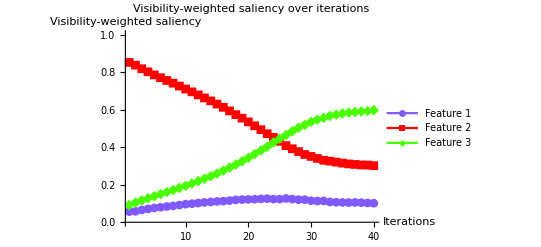

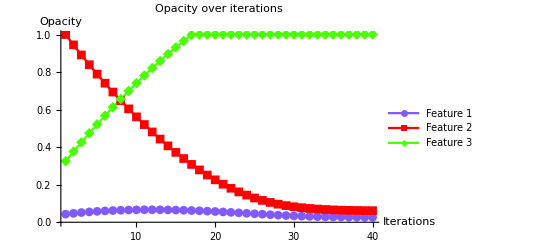

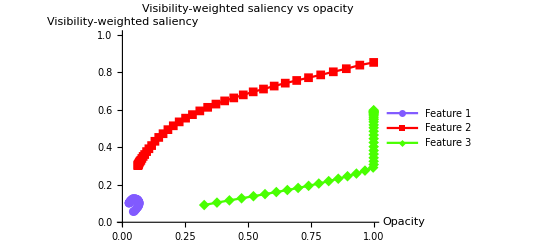

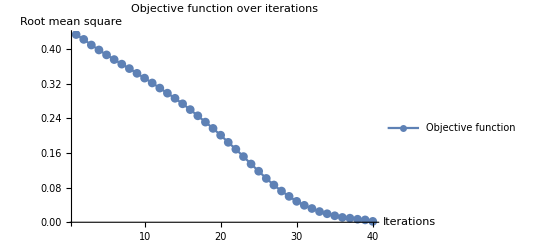

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | 
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | -0.0866924
1.10309
-1.01639
2 | 0.0581638
0.837143
0.104693 | 0.0474719
0.944846
0.37631 | 0.422533 | 0.00418362
-0.0537143
0.0495307 | -0.0836723
1.07429
-0.990614
3 | 0.0654655
0.817979
0.116555 | 0.0516555
0.891131
0.425841 | 0.409558 | 0.00345345
-0.0517979
0.0483445 | -0.0690689
1.03596
-0.96689
4 | 0.0708222
0.80149
0.127688 | 0.0551089
0.839333
0.474185 | 0.398088 | 0.00291778
-0.050149
0.0472312 | -0.0583556
1.00298
-0.944624
5 | 0.0762826
0.785044
0.138673 | 0.0580267
0.789184
0.521416 | 0.386718 | 0.00237174
-0.0485044
0.0461327 | -0.0474349
0.970088
-0.922653
6 | 0.0799996
0.77006
0.14994 | 0.0603985
0.74068
0.567549 | 0.375903 | 0.00200004
-0.047006
0.045006 | -0.0400008
0.94012
-0.900119
7 | 0.0837749
0.755361
0.160864 | 0.0623985
0.693674
0.612555 | 0.365357 | 0.00162251
-0.0455361
0.0439136 | -0.0324502
0.910721
-0.878271
8 | 0.0871895
0.741114
0.171697 | 0.064021
0.648138
0.656468 | 0.355053 | 0.00128105
-0.0441114
0.0428303 | -0.025621
0.882227
-0.856606
9 | 0.0916192
0.725596
0.182784 | 0.0653021
0.604027
0.699299 | 0.344128 | 0.000838084
-0.0425596
0.0417216 | -0.0167617
0.851193
-0.834431
10 | 0.0961713
0.709785
0.194044 | 0.0661401
0.561467
0.74102 | 0.333036 | 0.000382872
-0.0409785
0.0405956 | -0.00765743
0.81957
-0.811913
11 | 0.0989591
0.694723
0.206318 | 0.066523
0.520488
0.781616 | 0.321866 | 0.000104088
-0.0394723
0.0393682 | -0.00208175
0.789446
-0.787364
12 | 0.102156
0.678634
0.219211 | 0.0666271
0.481016
0.820984 | 0.310037 | -0.000215571
-0.0378634
0.0380789 | 0.00431142
0.757267
-0.761579
13 | 0.105694
0.662417
0.231888 | 0.0664115
0.443153
0.859063 | 0.298264 | -0.000569442
-0.0362417
0.0368112 | 0.0113888
0.724834
-0.736223
14 | 0.10825
0.646587
0.245163 | 0.0658421
0.406911
0.895874 | 0.286414 | -0.000825003
-0.0346587
0.0354837 | 0.0165001
0.693173
-0.709674
15 | 0.111029
0.629578
0.259393 | 0.0650171
0.372252
0.931358 | 0.273713 | -0.00110294
-0.0329578
0.0340607 | 0.0220588
0.659156
-0.681215
16 | 0.112599
0.612288
0.275113 | 0.0639141
0.339295
0.965419 | 0.260278 | -0.00125989
-0.0312288
0.0324887 | 0.0251977
0.624576
-0.649773
17 | 0.115403
0.593264
0.291332 | 0.0626543
0.308066
0.997907 | 0.245979 | -0.00154034
-0.0293264
0.0308668 | 0.0308068
0.586529
-0.617335
18 | 0.119169
0.57335
0.307482 | 0.0611139
0.278739
1. | 0.231412 | -0.00191686
-0.027335
0.0292518 | 0.0383372
0.546699
-0.585036
19 | 0.120713
0.554617
0.32467 | 0.0591971
0.251404
1. | 0.216845 | -0.0020713
-0.0254617
0.027533 | 0.0414261
0.509234
-0.55066
20 | 0.121703
0.534789
0.343507 | 0.0571258
0.225943
1. | 0.201151 | -0.00217035
-0.0234789
0.0256493 | 0.043407
0.469579
-0.512986
21 | 0.122797
0.513904
0.363299 | 0.0549554
0.202464
1. | 0.184664 | -0.00227972
-0.0213904
0.0236701 | 0.0455944
0.427808
-0.473403
22 | 0.124558
0.49332
0.382123 | 0.0526757
0.181073
1. | 0.168766 | -0.00245576
-0.019332
0.0217877 | 0.0491152
0.386639
-0.435754
23 | 0.125629
0.471666
0.402705 | 0.0502199
0.161741
1. | 0.151714 | -0.00256289
-0.0171666
0.0197295 | 0.0512578
0.343332
-0.39459
24 | 0.123313
0.451925
0.424762 | 0.047657
0.144575
1. | 0.134577 | -0.00233134
-0.0151925
0.0175238 | 0.0466268
0.30385
-0.350476
25 | 0.123347
0.431359
0.445295 | 0.0453257
0.129382
1. | 0.117946 | -0.00233465
-0.0131359
0.0154705 | 0.046693
0.262718
-0.309411
26 | 0.126664
0.408499
0.464837 | 0.0429911
0.116247
1. | 0.101245 | -0.00266642
-0.0108499
0.0135163 | 0.0533284
0.216997
-0.270326
27 | 0.123628
0.391589
0.484783 | 0.0403246
0.105397
1. | 0.0860656 | -0.00236277
-0.00915894
0.0115217 | 0.0472555
0.183179
-0.230434
28 | 0.120228
0.376422
0.503349 | 0.0379619
0.0962377
1. | 0.07209 | -0.00202284
-0.00764222
0.00966506 | 0.0404568
0.152844
-0.193301
29 | 0.120385
0.360899
0.518716 | 0.035939
0.0885955
1. | 0.0598087 | -0.00203845
-0.00608991
0.00812836 | 0.040769
0.121798
-0.162567
30 | 0.114544
0.350542
0.534913 | 0.0339006
0.0825056
1. | 0.0483128 | -0.00145444
-0.00505425
0.00650869 | 0.0290888
0.101085
-0.130174
31 | 0.112952
0.340083
0.546965 | 0.0324461
0.0774513
1. | 0.0391028 | -0.00129522
-0.00400827
0.00530349 | 0.0259043
0.0801655
-0.10607
32 | 0.113707
0.330202
0.556091 | 0.0311509
0.073443
1. | 0.0317706 | -0.00137072
-0.00302023
0.00439095 | 0.0274145
0.0604045
-0.087819
33 | 0.107998
0.325453
0.56655 | 0.0297802
0.0704228
1. | 0.024703 | -0.000799768
-0.00254526
0.00334503 | 0.0159954
0.0509052
-0.0669005
34 | 0.10629
0.3203
0.57341 | 0.0289804
0.0678776
1. | 0.0196529 | -0.000629029
-0.00203001
0.00265904 | 0.0125806
0.0406002
-0.0531808
35 | 0.105409
0.315047
0.579544 | 0.0283514
0.0658476
1. | 0.0149903 | -0.000540862
-0.00150474
0.0020456 | 0.0108172
0.0300948
-0.040912
36 | 0.104814
0.310572
0.584614 | 0.0278105
0.0643428
1. | 0.0111303 | -0.000481419
-0.00105715
0.00153857 | 0.00962838
0.021143
-0.0307714
37 | 0.105271
0.307924
0.586805 | 0.0273291
0.0632857
1. | 0.00939319 | -0.000527091
-0.000792442
0.00131953 | 0.0105418
0.0158488
-0.0263907
38 | 0.104417
0.305398
0.590186 | 0.026802
0.0624932
1. | 0.00695126 | -0.000441674
-0.00053975
0.000981424 | 0.00883348
0.010795
-0.0196285
39 | 0.102761
0.304817
0.592422 | 0.0263603
0.0619535
1. | 0.00542411 | -0.000276145
-0.000481704
0.000757848 | 0.0055229
0.00963407
-0.015157
40 | 0.101244
0.301616
0.59714 | 0.0260842
0.0614718
1. | 0.00202794 | -0.000124388
-0.000161601
0.000285988 | 0.00248775
0.00323201
-0.00571977

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity1=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_fixed.png",saliencyopacity1];
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_fixed.png",table1];
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

0.7187657

4

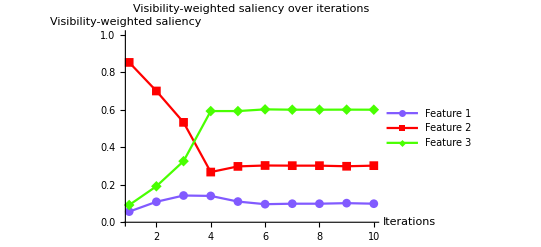

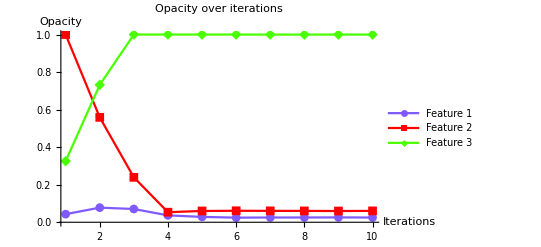

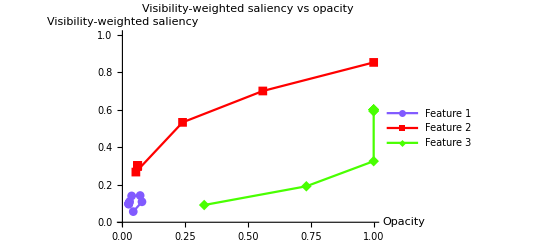

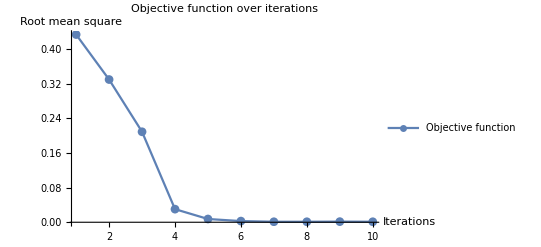

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902684
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532156
0.325404 | 0.0705927
0.239316
1. | 0.209046 | -0.00424397
-0.0232156
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.0366409
0.053591
1. | 0.0302658 | -0.00403004
0.00326374
0.000766303 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601185
1. | 0.00750894 | -0.00101697
0.000243727
0.00077324 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610934
1. | 0.00268296 | 0.000375446
-0.000235199
-0.000140248 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.060623
0.99972 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253827
0.0604703
0.999753 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 4
9 | 0.101768
0.298279
0.599953 | 0.0258579
0.0598593
0.999889 | 0.00142497 | -0.000176815
0.000172137
4.67825×10^-6 | 4
10 | 0.0988185
0.301546
0.599635 | 0.0251507
0.0605479
0.999908 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity2=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_parallelsearch.png",saliencyopacity2];
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_parallelsearch.png",table2];
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

1.18887

4

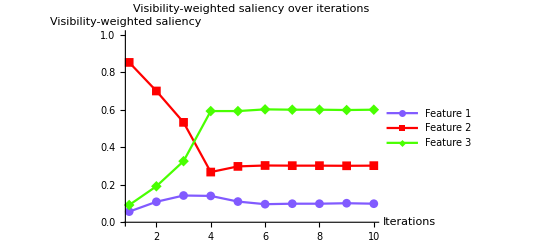

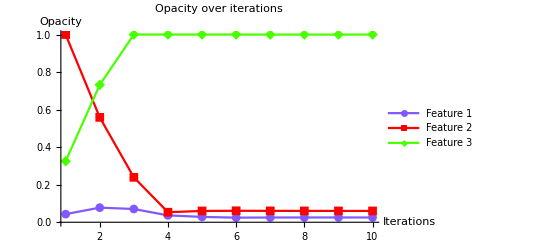

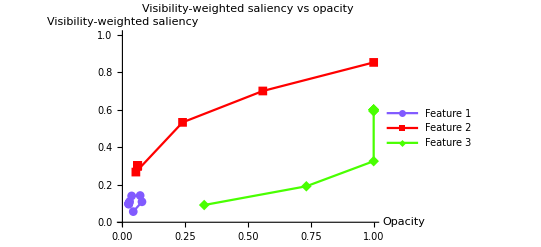

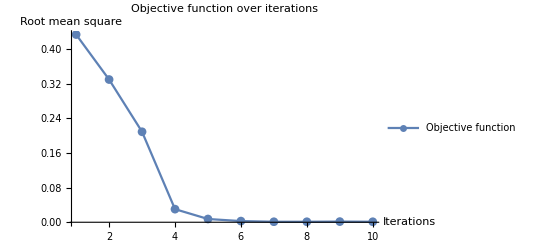

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.0566538
0.851543
0.0918031 | 0.0431373
1.
0.32549 | 0.433721 | 0.00433462
-0.0551543
0.0508197 | 8
2 | 0.109027
0.699312
0.191661 | 0.0778142
0.558766
0.732048 | 0.329784 | -0.000902684
-0.0399312
0.0408339 | 8
3 | 0.14244
0.532156
0.325404 | 0.0705927
0.239316
1. | 0.209046 | -0.00424397
-0.0232156
0.0274596 | 8
4 | 0.1403
0.267363
0.592337 | 0.0366409
0.053591
1. | 0.0302658 | -0.00403004
0.00326374
0.000766303 | 2
5 | 0.11017
0.297563
0.592268 | 0.0285809
0.0601185
1. | 0.00750894 | -0.00101697
0.000243727
0.00077324 | 4
6 | 0.0962455
0.302352
0.601402 | 0.024513
0.0610934
1. | 0.00268296 | 0.000375446
-0.000235199
-0.000140248 | 2
7 | 0.0988119
0.301527
0.599661 | 0.0252639
0.060623
0.99972 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
8 | 0.0988119
0.301527
0.599661 | 0.0253827
0.0604703
0.999753 | 0.00113426 | 0.000118811
-0.000152739
0.0000339274 | 1
9 | 0.10135
0.300759
0.597891 | 0.0255015
0.0603175
0.999787 | 0.00151034 | -0.00013496
-0.0000758946
0.000210854 | 1
10 | 0.0988185
0.301546
0.599635 | 0.0253665
0.0602416
0.999998 | 0.00114306 | 0.00011815
-0.000154621
0.0000364715 | 1

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
saliencyopacity3=ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
Export[NotebookDirectory[]<>dataname<>"_saliencyopacity_linesearch.png",saliencyopacity3];
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Objective function"},PlotLabel->"Objective function over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_linesearch.png",table3];
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

nucleon_strong_red→{{5.7333916,72,{0.0270685,0.0629737,1.}},{4.0059134,51,{0.0265144,0.0623885,1.}},{2.806498,37,{0.0260842,0.0614718,1.}},{0.7187657,4,{0.0251507,0.0605479,0.999908}},{1.18887,4,{0.0253665,0.0602416,0.999998}}}

```mathematica
ObjectiveFunction[pos_]:=RootMeanSquare[VisibilitySaliency[pos]-target];
```

```mathematica
(*ObjectiveFunction[{0.1,0.3,0.6}]
(*FindMinimum[{ObjectiveFunction[{x1,x2,x3}],0≤x1≤1,0≤x2≤1,0≤x3≤1},{{x1,{0.1}},{x2,{0.3}},{x3,{0.6}}}]*)
FindMinimum[x1 Cos[x1]+x2 Cos[x2],{{x1,0},{x2,0}}]
Plot3D[x1 Sin[x1]+x2 Sin[x2],{x1,0,10},{x2,0,10}]*)
```

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[NotebookDirectory[]<>dataname<>"_parameterspace.png",sp];
Export[NotebookDirectory[]<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics3D-

-Graphics3D-

-Graphics-

-Graphics-